```mathematica
<<MaTeX`
```

## Parámetros

```mathematica
(*HNL DECAYS TOO MESONS/LEPTONS*)(*ESTE SCRIPT GENERA LOS ARCHIVOS PCONFIG QUE UTILIZA PYTHIA8.*)(*NOTAR QUE SIEMPRE TOMA COMO ARGUMENTO LA MASA DEL HNL*)e=0.5109989461*10^-3;
mu=105.6583745*10^-3;
tau=1.77686;
leptons={e,mu,tau};
tfactor=1.5193*10^24(*Para pasar de s a GeV^-1*);mmc=3*10^11(*para pasar de s a mm/c*);ckm=({{0.9742,0.2243,0.0365},{0.218,0.997,0.0422},{0.0081,0.0394,1.019}});
gf=1.166378*10^-5;
xw=0.2223; (*sin^2(theta_w)*)
gll=-(1/2)+xw;
glr=xw;

(*charged pseudoscalar*)
d431={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],431};
d431bar={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],-431};
d411={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],411};
d411bar={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],-411};
k321={1.238*10^-8*tfactor,493.677*10^-3,155.6*10^-3,ckm[[1,2]]};
pi211={2.6*10^-8*tfactor,139.57061*10^-3,130.2*10^-3,ckm[[1,1]]};

(*Charged vector*)
k323={Null,895.55*10^-3,0.1827,ckm[[1,2]]}(*K*(892)*);
rho770c={Null,775.26*10^-3,0.162,ckm[[1,1]]};

(*neutral pseudoscalar*)
pi111={Null,134.977*10^-3,130.2*10^-3,Null};
eta221={Null,547.862*10^-3,81.7*10^-3,Null}(*eta*);eta331={Null,957.78*10^-3,-94.7*10^-3,Null}(*eta prime*);(*Neutral vector*)
rho770n={Null,775.26*10^-3,0.162,1-2xw};
omega782={Null,782.65*10^-3,0.153,4/3 xw};
phi1020={Null,1.019461,0.234,4/3 xw-1};

lambda[a_,b_,c_]:=a^2+b^2+c^2-2a*b-2a*c-2b*c;

i1[xu_,xd_,xl_]:=Re[12*NIntegrate[Re[1/x(x-xl^2-xd^2)(1+xu^2-x)√(lambda[x,xl^2,xd^2]*lambda[1,x,xu^2])],{x,(xd+xl)^2,(1-xu)^2}]];
```

## Funciones de Widths

```mathematica
5+3+3+2+3
```

16

### 1. (3.1) CC : N → l1 + nu2 l2

```mathematica
width1[l1_,l2_,n_,u_]:=If[n>l1+l2,Re[(gf^2 n^5)/(192 Pi^3)*u^2*i1[0,(l2/n),(l1/n)]],0];
enumumu[n_,u_]:=width1[e,mu,n,u];
enutautau[n_,u_]:=Re[width1[e,tau,n,u]UnitStep[n-e-tau]];
munuee[n_,u_]:=Re[width1[mu,e,n,u]UnitStep[n-mu-e]];
munutautau[n_,u_]:=Re[width1[mu,tau,n,u]UnitStep[n-mu-tau]];
taunuee[n_,u_]:=Re[width1[tau,e,n,u]UnitStep[n-tau-e]];
taunumumu[n_,u_]:=Re[width1[tau,mu,n,u]UnitStep[n-tau-mu]];
totalw1[n_,mixe_,mixmu_,mixtau_]:=enumumu[n,mixe]+enutautau[n,mixe]+munuee[n,mixmu]+munutautau[n,mixmu]+taunuee[n,mixtau]+taunumumu[n,mixtau];
Plot[totalw1[n,1,1,1],{n,0.1,2},PlotPoints->100];
```

### 2a. (3.4) NC: N → nu1 + f2 f2bar

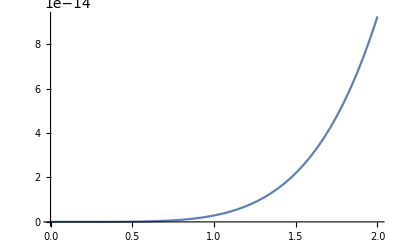

```mathematica
c1fa=1/4(1-4xw+8 xw^2);
c2fa=1/2 xw*(2*xw-1);
width2a[l_,n_,u_]:=If[n>2*l,
Module[{x,laux,g},
x=l/n;
g[t_]:=1-3 t^2-(1-t^2)√(1-4 t^2);
If[l==e, (* La masa del electrón es muy pequeña asi que usamos una serie de Taylor para g. *)
laux=Log[((D[g[t],{t,6}]/.t->0)/(6!)*(x)^6+(D[g[t],{t,8}]/.t->0)/(8!)*(x)^8+(D[g[t],{t,10}]/.t->0)/(10!)*(x)^10)/(x^2(1+√(1-4 x^2)))],
laux=Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))];];
Re[(gf^2 n^5)/(192 Pi^3)*u^2(c1fa((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+12 x^4(x^4-1)laux)+4c2fa(x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)laux))]],
0];
nuemumu[n_,u_]:=width2a[mu,n,u];
nuetautau[n_,u_]:=width2a[tau,n,u];
numuee[n_,u_]:=width2a[e,n,u];
numutautau[n_,u_]:=width2a[tau,n,u];
nutauee[n_,u_]:=width2a[e,n,u];
nutaumumu[n_,u_]:=width2a[mu,n,u];
totalw2a[n_,mixe_,mixmu_,mixtau_]:=nuemumu[n,mixe]+nuetautau[n,mixe]+numuee[n,mixmu]+numutautau[n,mixmu]+nutauee[n,mixtau]+nutaumumu[n,mixtau];
Plot[numuee[n,1],{n,0,2}]
```

### 2b. (3.4) NC+CC: N → nu1 + f1 f1bar

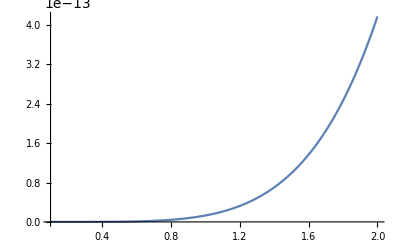

```mathematica
c1fb=1/4(1+4xw+8 xw^2);
c2fb=1/2 xw*(2*xw+1);
width2b[l_,n_,u_]:=If[n>2*l,Module[{x,laux,g},
x=l/n;
g[t_]:=1-3 t^2-(1-t^2)√(1-4 t^2);
If[l==e,
laux=Log[((D[g[t],{t,6}]/.t->0)/(6!)*(x)^6+(D[g[t],{t,8}]/.t->0)/(8!)*(x)^8+(D[g[t],{t,10}]/.t->0)/(10!)*(x)^10)/(x^2(1+√(1-4 x^2)))],
laux=Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))];];
Re[(gf^2 n^5)/(192 Pi^3)*u^2(c1fb((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+12 x^4(x^4-1)laux)+4c2fb(x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)laux))]],0];
nueee[n_,u_]:=width2b[e,n,u];
numumumu[n_,u_]:=width2b[mu,n,u];
nutautautau[n_,u_]:=width2b[tau,n,u];
totalw2b[n_,mixe_,mixmu_,mixtau_]:=nueee[n,mixe]+numumumu[n,mixmu]+nutautautau[n,mixtau];
Plot[nueee[n,1],{n,0.1,2},PlotPoints->100];
```

### 3a. (3.5) nu1 + nu2nu2bar

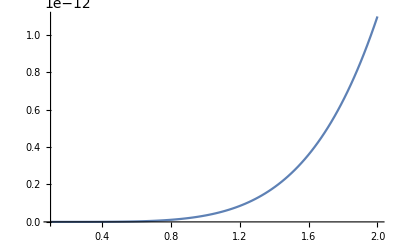

```mathematica
width3a[n_,u_]:=Re[(gf^2 n^5)/(768 Pi^3)u^2];
totalw3a[n_,mixe_,mixmu_,mixtau_]:=2*width3a[n,mixe]+2*width3a[n,mixmu]+2*width3a[n,mixtau];
Plot[totalw3a[n,1,1,1],{n,0.1,2},PlotPoints->100];
```

### 3b. (3.5) nu1 + nu1nu1bar

```mathematica
width3b[n_,u_]:=Re[(2*gf^2 n^5)/(768 Pi^3)u^2];
totalw3b[n_,mixe_,mixmu_,mixtau_]:=width3b[n,mixe]+width3b[n,mixmu]+width3b[n,mixtau];
Plot[totalw3b[n,1,1,1],{n,0.1,2},PlotPoints->100];
```

-Graphics-

### 4. (3.6) l- P+

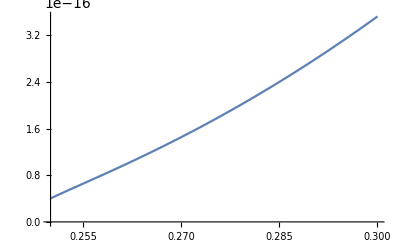

```mathematica
width4[meson_,l_,n_,u_]:=If[n>meson[[2]]+l,Module[{xl,xh},
xl=l/n;
xh=meson[[2]]/n;
Re[(gf^2 meson[[3]]^2 meson[[4]]^2 u^2 n^3)/(16Pi)((1-xl^2)^2-xh^2(1+xl^2))√lambda[1,xh^2,xl^2]]],0];
ePi[n_,u_]:=width4[pi211,e,n,u];
eK[n_,u_]:=width4[k321,e,n,u];
eD[n_,u_]:=width4[d411,e,n,u];
muPi[n_,u_]:=width4[pi211,mu,n,u];
muK[n_,u_]:=width4[k321,mu,n,u];
muD[n_,u_]:=width4[d411,mu,n,u];
tauPi[n_,u_]:=width4[pi211,tau,n,u];
tauK[n_,u_]:=width4[k321,tau,n,u];
tauD[n_,u_]:=width4[d411,tau,n,u];
totalw4[n_,mixe_,mixmu_,mixtau_]:=ePi[n,mixe]+eK[n,mixe]+eD[n,mixe]+muPi[n,mixmu]+muK[n,mixmu]+muD[n,mixmu]+tauPi[n,mixtau]+tauK[n,mixtau]+tauD[n,mixtau];
Plot[muPi[n,1],{n,0.25,0.3},PlotPoints->100]
```

### 5. (3.7) nu P0

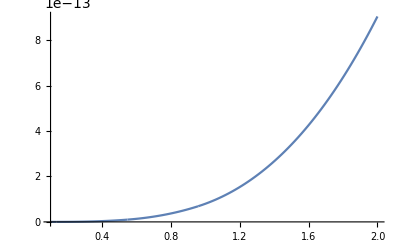

```mathematica
width5[meson_,n_,u_]:=If[n>meson[[2]],Module[{xh},
xh=meson[[2]]/n;
Re[(gf^2 meson[[3]]^2 n^3)/(32Pi)*u^2*(1-xh^2)^2]],0];
nupi0[n_,u_]:=width5[pi111,n,u];
nueta[n_,u_]:=width5[eta221,n,u];
nuetaprime[n_,u_]:=width5[eta331,n,u];
totalw5[n_,mixe_,mixmu_,mixtau_]:=nupi0[n,mixe]+nupi0[n,mixmu]+nupi0[n,mixtau]+nueta[n,mixe]+nueta[n,mixmu]+nueta[n,mixtau]+nuetaprime[n,mixe]+nuetaprime[n,mixmu]+nuetaprime[n,mixtau];
Plot[totalw5[n,1,1,1],{n,0.1,2},PlotPoints->100]
```

### 6. (3.8) l- V+

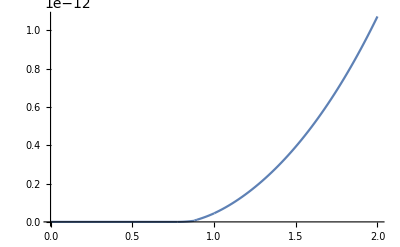

```mathematica
width6[meson_,l_,n_,u_]:=If[n>meson[[2]]+l,Module[{xl,xh},
xl=l/n;
xh=meson[[2]]/n;
Re[(gf^2*meson[[3]]^2 meson[[4]]^2 u^2 n^3)/(16Pi)((1-xl^2)^2+xh^2(1+xl^2)-2 xh^4)√lambda[1,xh^2,xl^2]]],0];
eKstar[n_,u_]:=width6[k323,e,n,u];
erhoc[n_,u_]:=width6[rho770c,e,n,u];
muKstar[n_,u_]:=width6[k323,mu,n,u];
murhoc[n_,u_]:=width6[rho770c,mu,n,u];
tauKstar[n_,u_]:=width6[k323,tau,n,u];
taurhoc[n_,u_]:=width6[rho770c,tau,n,u];
totalw6[n_,mixe_,mixmu_,mixtau_]:=eKstar[n,mixe]+erhoc[n,mixe]+muKstar[n,mixmu]+murhoc[n,mixmu]+tauKstar[n,mixtau]+taurhoc[n,mixtau];
Plot[{totalw6[n,1,1,1]},{n,0,2},PlotPoints->100]
```

### 7. (3.9) nu V0

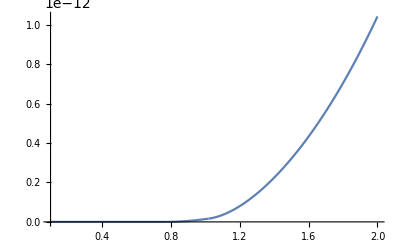

```mathematica
width7[meson_,n_,u_]:=If[n>meson[[2]],Module[{xh},
xh=meson[[2]]/n;
Re[(gf^2 meson[[4]]^2 meson[[3]]^2 u^2 n^3)/(32Pi)(1+2 xh^2)(1-xh^2)^2]],0];
nurho[n_,u_]:=width7[rho770n,n,u];
nuomega[n_,u_]:=width7[omega782,n,u];
nuphi[n_,u_]:=width7[phi1020,n,u];
totalw7[n_,mixe_,mixmu_,mixtau_]:=nurho[n,mixe]+nurho[n,mixmu]+nurho[n,mixtau]+nuomega[n,mixe]+nuomega[n,mixmu]+nuomega[n,mixtau]+nuphi[n,mixe]+nuphi[n,mixmu]+nuphi[n,mixtau];
Plot[totalw7[n,1,1,1],{n,0.1,2},PlotPoints->100]
```

### Totalw

```mathematica
totalw[n_,mixe_,mixmu_,mixtau_]:=totalw1[n,mixe,mixmu,mixtau]+totalw2a[n,mixe,mixmu,mixtau]+totalw2b[n,mixe,mixmu,mixtau]+totalw3a[n,mixe,mixmu,mixtau]+totalw3b[n,mixe,mixmu,mixtau]+totalw4[n,mixe,mixmu,mixtau]+totalw5[n,mixe,mixmu,mixtau]+totalw6[n,mixe,mixmu,mixtau]+totalw7[n,mixe,mixmu,mixtau]
```

## Plots Debug

### Plots CC

```mathematica
tablecanalesCC[n_]:={Null,Null,eK[n,1],muK[n,1],erhoc[n,1],Null,eKstar[n,1],muKstar[n,1],eD[n,1],(enumumu[n,1]+munuee[n,1]),(enutautau[n,1]+taunuee[n,1]),tauPi[n,1],(munutautau[n,1]+taunumumu[n,1])};
tablecanalesNC[n_]:={(totalw3a[n,1,1,1]+totalw3b[n,1,1,1]),(nueee[n,1]+numuee[n,1]+nutauee[n,1]),
(numumumu[n,1]+nuemumu[n,1]+nutaumumu[n,1]),3*nupi0[n,1],3*nurho[n,1],3*nuomega[n,1],3*nueta[n,1],3*nuetaprime[n,1],3*nuphi[n,1]}
```

```mathematica
plottheme = "Scientific";
scalingfunctions = {"Linear", "Log"};
plotrange = {{0, 2}, {10^-5, 1}};
imagesize={400,Automatic};
```

```mathematica
coloursCC={Darker[Green,0.4],Darker[Green,0.4],Red,Red,Lighter[Orange,0.2],Lighter[Orange,0.2],Lighter[Blue,0.4],Lighter[Blue,0.4],Darker[Cyan,0.2],Purple,Yellow,Black,Pink};
stylesCC={Automatic,Dashed,Automatic,Dashed,Automatic,Dashed,Automatic,Dashed,Automatic,Automatic,Automatic,Automatic,Automatic};
legendsCC={"ePi","muPi","eK","muK","erhoc","murhoc","eKstar","muKstar","eD","nuemu","nuetau","taupi","numutau"};
coloursNC={Purple,Darker[Green,0.4],Darker[Green,0.4],Darker[Cyan,0.2],Lighter[Orange,0.2],Lighter[Blue,0.3],Red,Red,Black};
stylesNC={Automatic,Automatic,Dashed,Automatic,Automatic,Automatic,Automatic,Dashed,Automatic};
legendsNC={"nununu","nuee","numumu","nupi0","nurho0","nuomega","nueta","nuetaprime","nuphi"};
bg = Plot[Null, {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200];
```

### Plots CC

```mathematica
plotpointsCC=400;
plotsCC={};
Do[
plotaux=Plot[{(tablecanalesCC[n][[i]])/totalw[n,1,1,1]},{n,0.01,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->plotpointsCC,PlotStyle->{coloursCC[[i]],stylesCC[[i]]}];
AppendTo[plotsCC,plotaux];
,{i,1,Length@coloursCC}];
plotsCCexp=Show[plotsCC];
```

D::dvar: Multiple derivative specifier {t,6.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,6.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {t,8.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

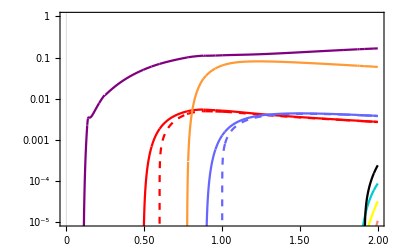

```mathematica
Show[bg,plotsCCexp]
```

### Plots NC

```mathematica
plotpointsNC=400;
plotsNC={};
Do[
plotaux=Plot[{(tablecanalesNC[n][[i]])/totalw[n,1,1,1]},{n,0.01,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->plotpointsNC,PlotStyle->{coloursNC[[i]],stylesNC[[i]]}];
AppendTo[plotsNC,plotaux];
,{i,1,Length@coloursNC}];
plotsNCexp=Show[plotsNC]
```

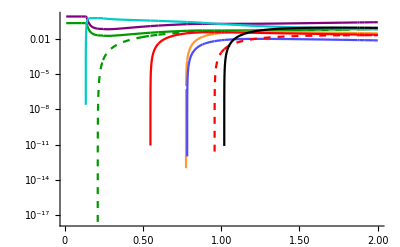

```mathematica
plotsNCexp
```

### Aux Plots

```mathematica
auxePi=Plot[ePi[n,1]/totalw[n,1,1,1],{n,0.1,0.2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->2000,PlotTheme->"Scientific",PlotStyle->Darker[Green,0.4]];
```

```mathematica
auxmuPi=Plot[muPi[n,1]/totalw[n,1,1,1],{n,0.245,0.255},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->16000,PlotTheme->"Scientific",PlotStyle->{Darker[Green,0.4],Dashed}]
```

```mathematica
auxmuPi2=Plot[muPi[n,1]/totalw[n,1,1,1],{n,0.255,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->100,PlotTheme->"Scientific",PlotStyle->{Darker[Green,0.4],Dashed}]
```

```mathematica
auxePi2=Plot[ePi[n,1]/totalw[n,1,1,1],{n,0.2,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->Automatic,PlotTheme->"Scientific",PlotStyle->Darker[Green,0.4]]
```

```mathematica
auxmurhoc=Plot[murhoc[n,1]/totalw[n,1,1,1],{n,0.85,0.9},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->3000,PlotTheme->"Scientific",PlotStyle->{Lighter[Orange,0.2],Dashed}];
```

```mathematica
auxmurhoc2=Plot[murhoc[n,1]/totalw[n,1,1,1],{n,0.9,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->3000,PlotTheme->"Scientific",PlotStyle->{Lighter[Orange,0.2],Dashed}];
```

```mathematica
auxplotsCC={auxePi,auxePi2,auxmuPi,auxmuPi2,auxmurhoc,auxmurhoc2};
```

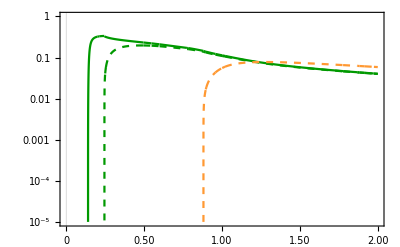
```mathematica
auxplotsCCexp=-Graphics-;
```

# Tweak Plots

```mathematica
magnificationlegends=0.9;
magnificationlabels=1;
latexePi=MaTeX["e^{\\mp}\\pi^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexemuPi=MaTeX["\\mu^{\\mp}\\pi^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexeK=MaTeX["e^{\\mp} K^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexmuK=MaTeX["\\mu^{\\mp} K^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexerhoc=MaTeX["e^{\\mp} \\rho^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexmurhoc=MaTeX["\\mu^{\\mp} \\rho^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexeKstar=MaTeX["e^{\\mp} K^{*\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexmuKstar=MaTeX["\\mu^{\\mp} K^{*\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexeD=MaTeX["e^{\\mp} D^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexnuxemu=MaTeX["\\nu e^{\\mp} \\mu^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexnuxetau=MaTeX["e^{\\mp} \\tau^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latextauPi=MaTeX["\\tau^{\\mp} \pi^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexnuxmutau=MaTeX["\\nu \\mu^{\\mp} \\tau^{\\pm}",Magnification->magnificationlegends,ContentPadding->False];
latexnununu=MaTeX["\\nu \\nu \\nu ",Magnification->magnificationlegends,ContentPadding->False];
latexnuxee=MaTeX["\\nu e^+ e^- ",Magnification->magnificationlegends,ContentPadding->False];
latexnuxmumu=MaTeX["\\nu \\mu^+ \\mu^- ",Magnification->magnificationlegends,ContentPadding->False];
latexnuxpi0=MaTeX["\\nu \\pi^0 ",Magnification->magnificationlegends,ContentPadding->False];
latexnuxrho0=MaTeX["\\nu \\rho^0 ",Magnification->magnificationlegends,ContentPadding->False];
latexnuxomega=MaTeX["\\nu \\omega",Magnification->magnificationlegends,ContentPadding->False];
latexnuxeta=MaTeX["\\nu \\eta ",Magnification->magnificationlegends,ContentPadding->False];
latexnuxetaprime=MaTeX["\\nu \\eta'",Magnification->magnificationlegends,ContentPadding->False];
latexnuxphi=MaTeX["\\nu \\phi",Magnification->magnificationlegends,ContentPadding->False];
legendsCC={latexePi,latexemuPi,latexeK,latexmuK,latexerhoc,latexmurhoc,latexeKstar,latexmuKstar,latexeD,latexnuxemu,latexnuxetau,latextauPi,latexnuxmutau};
legendsNC={latexnununu,latexnuxee,latexnuxmumu,latexnuxpi0,latexnuxrho0,latexnuxomega,latexnuxeta,latexnuxetaprime,latexnuxphi};
latexlabelx=MaTeX["\\text{HNL mass (GeV)}",Magnification->magnificationlabels,ContentPadding->False]
latexlabely=MaTeX["\\Gamma_i/\\Gamma_{\\text{TOT}}",Magnification->magnificationlabels,ContentPadding->False];
```

Syntax::stresc: Unknown string escape \p.

-Graphics-

## CC

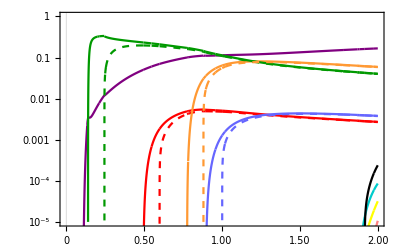

/home/sane/mainhnlchain/hnlchain/otherplots/brplots/plotCC.pdf

```mathematica
imagesize={400,Automatic};
plotlegendsCC=Placed[LineLegend[Join[Table[{coloursCC[[i]],stylesCC[[i]]},{i,1,Length@coloursCC}],{Null}],Table[legendsCC[[i]],{i,1,Length@legendsCC}],Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->12
],{0.75,0.25}];
ticksx=Automatic;
ticksy1={};
Do[
ticksy1=Join[ticksy1,Table[{i*10^(-5+j),"",{0.005,0.0}},{i,1,9}]];
,{j,0,5}]
ticksy2={{10^-5,"10^-5",{0.01,0.0}},{10^-4,"10^-4",{0.01,0.0}},{10^-3,"10^-3",{0.01,0.0}},{10^-2,"10^-2",{0.01,0.0}},{10^-1,"10^-1",{0.01,0.0}},{1,"1",{0.01,0.0}}};
ticksy=Join[ticksy1,ticksy2];
ticks={{ticksy,Automatic},{ticksx,Automatic}};
framelabel={latexlabelx,latexlabely};
bg = Plot[Table[Null,{i,1,Length@coloursCC}], {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200,PlotLegends->plotlegendsCC,PlotStyle->{Dashed},FrameTicks->ticks,FrameLabel->framelabel];finaplotCC=Show[bg,plotsCC,auxplotsCC,PlotRangeClipping->True]
Export[NotebookDirectory[]<>"plotCC.pdf",finaplotCC,ImageResolution->300]
```

## NC

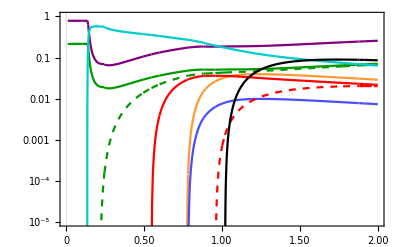

/home/sane/mainhnlchain/hnlchain/otherplots/brplots/plotNC.png

```mathematica
imagesize={400,Automatic};
plotlegendsNC=Placed[LineLegend[Join[Table[{coloursNC[[i]],stylesNC[[i]]},{i,1,Length@coloursNC}],{Null}],Table[legendsNC[[i]],{i,1,Length@legendsNC}],Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->12
],{0.75,0.3}];
ticksx=Automatic;
ticksy1={};
Do[
ticksy1=Join[ticksy1,Table[{i*10^(-5+j),"",{0.005,0.0}},{i,1,9}]];
,{j,0,5}]
ticksy2={{10^-5,"10^-5",{0.01,0.0}},{10^-4,"10^-4",{0.01,0.0}},{10^-3,"10^-3",{0.01,0.0}},{10^-2,"10^-2",{0.01,0.0}},{10^-1,"10^-1",{0.01,0.0}},{1,"1",{0.01,0.0}}};
ticksy=Join[ticksy1,ticksy2];
ticks={{ticksy,Automatic},{ticksx,Automatic}};
framelabel={latexlabelx,latexlabely};
bg = Plot[Table[Null,{i,1,Length@coloursCC}], {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200,PlotLegends->plotlegendsNC,PlotStyle->{Dashed},FrameTicks->ticks,FrameLabel->framelabel];finaplotNC=Show[bg,plotsNCexp,PlotRangeClipping->True]
Export[NotebookDirectory[]<>"plotNC.png",finaplotNC,ImageResolution->300]
```

-Graphics-

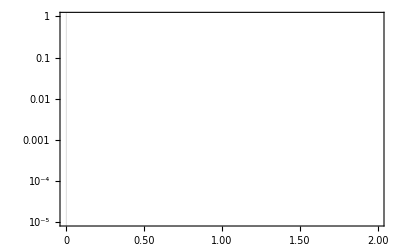

```mathematica
magnificationlabels=1;
latexlabelx=MaTeX["\\text{HNL mass (GeV)}",Magnification->magnificationlabels,ContentPadding->False]
latexlabely=MaTeX["\\Gamma_i/\\Gamma_{\\text{TOT}}",Magnification->magnificationlabels,ContentPadding->False];
framelabel={latexlabelx,latexlabely};
bg = Plot[Table[Null,{i,1,Length@coloursCC}], {x, 0.01, 2}, PlotTheme -> plottheme, ScalingFunctions -> scalingfunctions, PlotRange -> plotrange,ImageSize->imagesize,PlotPoints->200,PlotLegends->plotlegendsNC,PlotStyle->{Dashed},FrameTicks->ticks,FrameLabel->framelabel]
```